## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = False;
removeOutputFiles = False;

rxnName="FBP2";
fitLabel="new_lma_3";
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)


(* user will need to change this path *)
pathMASSef = "/home/mrama/Desktop/MASSef/";
kineticDataFileName =  "kinetic_data_MASSef.csv";

mainFolder = "fit_FBP2";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

True

Working dir:/home/mrama/Dropbox/MASSef/examples/FBP2/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

{fdp,Null,Keq substrate}

{41.5,Keq value}

{{{fdp,Null}},kcat substrates}

{5.7,kcat value}

{{{fdp,0.00006},{pep,0.001}},kcat substrates}

{3.22,kcat value}

{{{fdp,0.00005},{atp,0.00125}},kcat substrates}

{1.67,kcat value}

{{{fdp,0.00005},{adp,0.00125}},kcat substrates}

{0.949,kcat value}

{{{fdp,0.00005},{adp,0.0019}},kcat substrates}

{0.72,kcat value}

{fdp,Km or S05 substrate}

{0.00007,Km or S05 value}

{fdp,Other parameter susbtrate}

{2.05,Other parameter value}

{f1p,Inhibition or activation constant substrate}

{0.001,Inhibition or activation constant value}

{pi,Inhibition or activation constant substrate}

{0.00035,Inhibition or activation constant value}

(fdp^c+h2o^c→f6p^c+pi^c)^FBP2

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp,Null | 41.5 | 39.425
43.575 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | 0.00007 | 0.000068
0.000072 |  | M | 9 | 37 | chesk | 0.5 | mn2 | 0.002
cl | 0.004

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 5.7 | 5.6
5.8 | 1/s | 9 | 37 | chesk | 0.5 | mn2 | 0.002
cl | 0.004
1 | fdp | 0.00006
pep | 0.001 | 9.66905 | 9.1856
10.1525 | 1/s | 7.7 | 37 | tric | 0.02 | mn2 | 0.001
cl | 0.002
1 | fdp | 0.00005
atp | 0.00125 | 5.01469 | 4.76396
5.26543 | 1/s | 7.7 | 37 | tric | 0.02 | mn2 | 0.001
1 | fdp | 0.00005
adp | 0.00125 | 2.84967 | 2.70718
2.99215 | 1/s | 7.7 | 37 | tric | 0.02 | mn2 | 0.001
1 | fdp | 0.00005
adp | 0.0019 | 2.16202 | 2.05392
2.27013 | 1/s | 7.7 | 37 | tric | 0.02 | mn2 | 0.001

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | f1p | 0.001 | 0.00095
0.00105 |  | Competitive | fdp | 0.00007 | M | 7.7 | 25 | tric | 0.02 | mn2 | 0.001
cl | 0.002
1 | Kic | pi | 0.00035 | 0.0003325
0.0003675 |  | Competitive | fdp | 0.00007 | M | 7.7 | 25 | tric | 0.02 | mn2 | 0.001
cl | 0.002

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | n | fdp | 2.05 | 2.
2.1 |  |  | 9 | 37 | chesk | 0.5 | mn2 | 0.002
cl | 0.004

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {};
s05Priorities = {1};
kcatPriorities = {1,0,0,0,0};
inhibitionPriorities={0,0};
activationPriorities = Null;
otherParamsPriorities = {1};


{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(fdp^c+h2o^c→f6p^c+pi^c)^FBP2

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp,Null | 41.5 | 39.425
43.575 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | 0.00007 | 0.000068
0.000072 |  | M | 9 | 37 | chesk | 0.5 | mn2 | 0.002
cl | 0.004

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 5.7 | 5.6
5.8 | 1/s | 9 | 37 | chesk | 0.5 | mn2 | 0.002
cl | 0.004

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | n | fdp | 2.05 | 2.
2.1 |  |  | 9 | 37 | chesk | 0.5 | mn2 | 0.002
cl | 0.004

## Construct Module and Set Up Comparison Equations

### Construct enzyme module

```mathematica
enz ="E_FBP2[c]"
substrateList ={"fdp"};
productList={"pi", "f6p"};
nActiveSites = 2;
bindingReversibility = " <=> ";
releaseReversibility = " <=> ";
transitionReversibility = "<=> ";

catalyticBranch =generateOrderedMechanism[enz, substrateList,  productList, nActiveSites, bindingReversibility, 
						transitionReversibility, releaseReversibility] ;

enzymeModelOrig=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->1,Inhibitors->{},InhibitionSites->1];

catalyticBranch//TableForm
enzymeModelOrig["Reactions"]
```

E_FBP2[c]

E_FBP2[c] + fdp[c] <=> E_FBP2[c]&fdp
E_FBP2[c]&fdp + fdp[c] <=> E_FBP2[c]&fdp&fdp
E_FBP2[c]&fdp&fdp<=> E_FBP2[c]&pi&pi&f6p&f6p
E_FBP2[c]&pi&pi&f6p&f6p <=> E_FBP2[c]&pi&pi&f6p + f6p[c]
E_FBP2[c]&pi&pi&f6p <=> E_FBP2[c]&pi&pi + f6p[c]
E_FBP2[c]&pi&pi <=> E_FBP2[c]&pi + pi[c]
E_FBP2[c]&pi <=> E_FBP2[c] + pi[c]

{((FBP2^c)_^+fdp^c⇌(FBP2^c&fdp^c)_^)^FBP21,((FBP2^c&pi^c)_^⇌(FBP2^c)_^+pi^c)^FBP22,((FBP2^c&fdp^c)_^+fdp^c⇌(FBP2^c&fdp^c&fdp^c)_^)^FBP23,((FBP2^c&pi^c&pi^c)_^⇌(FBP2^c&pi^c)_^+pi^c)^FBP24,((FBP2^c&fdp^c&fdp^c)_^⇌(FBP2^c&pi^c&pi^c&f6p^c&f6p^c)_^)^FBP25,((FBP2^c&pi^c&pi^c&f6p^c)_^⇌(FBP2^c&pi^c&pi^c)_^+f6p^c)^FBP26,((FBP2^c&pi^c&pi^c&f6p^c&f6p^c)_^⇌(FBP2^c&pi^c&pi^c&f6p^c)_^+f6p^c)^FBP27}

### Define all catalytic tracks

```mathematica
catalyticReactionsSetsList = {enzymeModelOrig["Reactions"]};
```

## Set up rate equations

```mathematica
deleteDirectoryContents[inputPath];
```

```mathematica
MWCFlag=False;
nActiveSites=2;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModelOrig, rxn, rxnName, inputPath, {},{}, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

{fdp^c→0}

{f6p^c→0,pi^c→0}

{fdp^c→1}

{f6p^c→1,pi^c→1}

Added inhibition reactions:

{}

Loading flux equation...

Loading absolute rate forward equation...

Loading absolute rate reverse equation...

Loading relative rate forward equation...

Loading relative rate reverse equation...

Loading relative rate reverse equation...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

```mathematica
enzymeModel["Reactions"]
```

{((FBP2^c)_^+fdp^c⇌(FBP2^c&fdp^c)_^)^FBP21,((FBP2^c&pi^c)_^⇌(FBP2^c)_^+pi^c)^FBP22,((FBP2^c&fdp^c)_^+fdp^c⇌(FBP2^c&fdp^c&fdp^c)_^)^FBP23,((FBP2^c&pi^c&pi^c)_^⇌(FBP2^c&pi^c)_^+pi^c)^FBP24,((FBP2^c&fdp^c&fdp^c)_^⇌(FBP2^c&pi^c&pi^c&f6p^c&f6p^c)_^)^FBP25,((FBP2^c&pi^c&pi^c&f6p^c)_^⇌(FBP2^c&pi^c&pi^c)_^+f6p^c)^FBP26,((FBP2^c&pi^c&pi^c&f6p^c&f6p^c)_^⇌(FBP2^c&pi^c&pi^c&f6p^c)_^+f6p^c)^FBP27}

```mathematica
absoluteRateForward
```

(2 (fdp^c)^2 FBP2_total_Global k_FBP21^⟶ k_FBP22^⟶ k_FBP23^⟶ k_FBP24^⟶ k_FBP25^⟶ k_FBP26^⟶ k_FBP27^⟶)/(k_FBP21^⟵ k_FBP22^⟶ k_FBP24^⟶ k_FBP26^⟶ (k_FBP25^⟶ k_FBP27^⟶+k_FBP23^⟵ (k_FBP25^⟵+k_FBP27^⟶))+fdp^c (k_FBP22^⟶ k_FBP23^⟶ k_FBP24^⟶ k_FBP25^⟶ k_FBP26^⟶ k_FBP27^⟶+k_FBP21^⟶ (fdp^c k_FBP23^⟶ k_FBP24^⟶ k_FBP25^⟶ k_FBP26^⟶ k_FBP27^⟶+k_FBP22^⟶ (k_FBP24^⟶ k_FBP25^⟶ k_FBP26^⟶ k_FBP27^⟶+k_FBP23^⟵ k_FBP24^⟶ k_FBP26^⟶ (k_FBP25^⟵+k_FBP27^⟶)+fdp^c k_FBP23^⟶ (k_FBP25^⟶ k_FBP26^⟶ k_FBP27^⟶+k_FBP24^⟶ (k_FBP25^⟵ k_FBP26^⟶+k_FBP26^⟶ k_FBP27^⟶+k_FBP25^⟶ (k_FBP26^⟶+k_FBP27^⟶)))))))

```mathematica
relativeRateForward[[1]]
```

((fdp^c)^2 (k_FBP22^⟶ k_FBP23^⟶ k_FBP24^⟶ k_FBP25^⟶ k_FBP26^⟶ k_FBP27^⟶+k_FBP21^⟵ k_FBP22^⟶ k_FBP24^⟶ k_FBP26^⟶ (k_FBP25^⟶ k_FBP27^⟶+k_FBP23^⟵ (k_FBP25^⟵+k_FBP27^⟶))+k_FBP21^⟶ (k_FBP23^⟶ k_FBP24^⟶ k_FBP25^⟶ k_FBP26^⟶ k_FBP27^⟶+k_FBP22^⟶ (k_FBP24^⟶ k_FBP25^⟶ k_FBP26^⟶ k_FBP27^⟶+k_FBP23^⟵ k_FBP24^⟶ k_FBP26^⟶ (k_FBP25^⟵+k_FBP27^⟶)+k_FBP23^⟶ (k_FBP25^⟶ k_FBP26^⟶ k_FBP27^⟶+k_FBP24^⟶ (k_FBP25^⟵ k_FBP26^⟶+k_FBP26^⟶ k_FBP27^⟶+k_FBP25^⟶ (k_FBP26^⟶+k_FBP27^⟶)))))))/(k_FBP21^⟵ k_FBP22^⟶ k_FBP24^⟶ k_FBP26^⟶ (k_FBP25^⟶ k_FBP27^⟶+k_FBP23^⟵ (k_FBP25^⟵+k_FBP27^⟶))+fdp^c (k_FBP22^⟶ k_FBP23^⟶ k_FBP24^⟶ k_FBP25^⟶ k_FBP26^⟶ k_FBP27^⟶+k_FBP21^⟶ (fdp^c k_FBP23^⟶ k_FBP24^⟶ k_FBP25^⟶ k_FBP26^⟶ k_FBP27^⟶+k_FBP22^⟶ (k_FBP24^⟶ k_FBP25^⟶ k_FBP26^⟶ k_FBP27^⟶+k_FBP23^⟵ k_FBP24^⟶ k_FBP26^⟶ (k_FBP25^⟵+k_FBP27^⟶)+fdp^c k_FBP23^⟶ (k_FBP25^⟶ k_FBP26^⟶ k_FBP27^⟶+k_FBP24^⟶ (k_FBP25^⟵ k_FBP26^⟶+k_FBP26^⟶ k_FBP27^⟶+k_FBP25^⟶ (k_FBP26^⟶+k_FBP27^⟶)))))))

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModelOrig,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

```mathematica
FilePrint@dataPathList
```

Priority	f6p[c]	fdp[c]	pi[c]	param_FBP2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/input/haldaneRatio_1.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/input/haldaneRatio_1.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/input/haldaneRatio_1.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/input/haldaneRatio_1.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/input/haldaneRatio_1.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/input/haldaneRatio_1.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/input/haldaneRatio_1.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/input/haldaneRatio_1.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/input/haldaneRatio_1.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/input/haldaneRatio_1.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/input/haldaneRatio_1.txt"	41.5
1	0	7.000000000000002e-6	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/input/relRateFor_fdp.txt"	0.00883377824981335
1	0	0.000011094252347227801	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/input/relRateFor_fdp.txt"	0.022395622457170455
1	0	0.00001758320502056708	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/input/relRateFor_fdp.txt"	0.055609816758203534
1	0	0.000027867501938744792	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/input/relRateFor_fdp.txt"	0.1314590000241482
1	0	0.000044167014113613516	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/input/relRateFor_fdp.txt"	0.28008099405284803
1	0	0.00007000000000000002	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/input/relRateFor_fdp.txt"	0.5000000000000001
1	0	0.00011094252347227801	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/input/relRateFor_fdp.txt"	0.7199190059471522
1	0	0.0001758320502056708	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/input/relRateFor_fdp.txt"	0.8685409999758519
1	0	0.0002786750193874482	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/input/relRateFor_fdp.txt"	0.9443901832417967
1	0	0.0004416701411361352	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/input/relRateFor_fdp.txt"	0.9776043775428295
1	0	0.0007000000000000001	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/input/relRateFor_fdp.txt"	0.9911662217501868
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/input/absRateFor.txt"	5.7

### Simulate data with uncertainty

```mathematica
Export["GAPDSimulateDataWithUncertaintyArguments.mx",{nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList}, "MX"];

Export["GAPDSimulateDataWithUncertaintyResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

«7 more identical outputs»

```mathematica
FilePrint[dataPathList[[1]]]
```

13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.09090909090909095
0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.1368068886032101
0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.20076000891310197
0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.2847472489508014
0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.38686317984685703
0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.5000000000000001
0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.6131368201531432
0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7152527510491988
0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7992399910868984
0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.86319311139679
0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.9090909090909091
0	0.00010091718583050879	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.09090909090909087
0	0.0001599429608251066	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.13680688860321003
0	0.0002534925097937858	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2007600089131016
0	0.0004017585531120535	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2847472489508014
0	0.0006367443958403206	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.386863179846857
0	0.001009171858305088	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.4999999999999999
0	0.001599429608251066	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.613136820153143
0	0.0025349250979378583	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7152527510491984
0	0.0040175855311205344	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7992399910868982
0	0.006367443958403205	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.8631931113967901
0	0.01009171858305088	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.9090909090909091
0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.0909090909090909
0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.13680688860321005
0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.20076000891310167
0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.2847472489508014
0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.3868631798468568
0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.5
0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.6131368201531432
0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7152527510491987
0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7992399910868982
0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.86319311139679
0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.9090909090909091
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
Export["GAPDParameterScanArguments.mx",{paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList}, "MX"];

Export["GAPDParameterScanResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

«18 more identical outputs»

```mathematica
FilePrint[dataPathList[[18]]]
```

13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.09090909090909095
0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.13680688860321014
0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.20076000891310194
0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.28474724895080133
0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.386863179846857
0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.5000000000000002
0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.6131368201531432
0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7152527510491989
0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7992399910868984
0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.86319311139679
0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.9090909090909093
0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.090909090909091
0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.1368068886032102
0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2007600089131019
0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2847472489508017
0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.3868631798468571
0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.5000000000000003
0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.6131368201531434
0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7152527510491988
0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7992399910868984
0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.86319311139679
0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.9090909090909092
0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.09090909090909094
0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.13680688860321008
0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.20076000891310175
0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.2847472489508015
0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.3868631798468569
0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.5
0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.6131368201531432
0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7152527510491988
0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7992399910868982
0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.8631931113967899
0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.9090909090909092
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=100;
numCPUs=1;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel, numCPUs];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel,numCPUs];
```

## Run the Fitting Algorithms

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numTrials, dataPathList]
```

best_fit: 0.70551373402
best_fit: 0.753733950725
best_fit: 0.7561990401
best_fit: 0.849889488936
best_fit: 0.877451108863
best_fit: 0.906022105619
best_fit: 0.65208137079
best_fit: 1.05985428945
best_fit: 1.05087745441
best_fit: 1.48996112552
best_fit: 0.487130172316
best_fit: 0.677285811696
best_fit: 2.96627401097
best_fit: 0.192967775809
best_fit: 1.00479270468
best_fit: 86.0710602646
best_fit: 1.07662259371
best_fit: 0.84275051738
best_fit: 1.06442422014
best_fit: 0.674215182626
best_fit: 1.07314200391
best_fit: 0.930782535429
best_fit: 1.09537884894
best_fit: 0.895151291072
best_fit: 0.401399691203
best_fit: 1.09775041608
best_fit: 1.06457016148
best_fit: 0.769724176868
best_fit: 0.991152456529
best_fit: 0.525952269149
best_fit: 1.09687354823
best_fit: 0.533358166923
best_fit: 1.01970810459
best_fit: 0.678410926039
best_fit: 1.09236085974
best_fit: 0.95939534977
best_fit: 0.920178229057
best_fit: 0.663024335863
best_fit: 0.987600225338
best_fit: 0.541081391746
best_fit: 0.901326440516
best_fit: 0.631245365058
best_fit: 0.575629182176
best_fit: 0.928897441691
best_fit: 0.921282460322
best_fit: 1.01715768564
best_fit: 0.948520920449
best_fit: 0.573886367334
best_fit: 0.907081297961
best_fit: 1.08142174266
best_fit: 1.06227666391
best_fit: 0.671503509652
best_fit: 0.573780982641
best_fit: 0.951138583603
best_fit: 1.07912475682
best_fit: 1.09533800438
best_fit: 1.07491230472
best_fit: 1.09339237438
best_fit: 0.27143245322
best_fit: 0.729319199745
best_fit: 0.76373268546
best_fit: 1.07232759991
best_fit: 1.92696943945
best_fit: 0.802280790978
best_fit: 0.750796797865
best_fit: 0.904905844612
best_fit: 1.08391434897
best_fit: 0.877924330578
best_fit: 0.843091316108
best_fit: 0.761451553259
best_fit: 0.610292511525
best_fit: 0.684550333616
best_fit: 1.08681521365
best_fit: 0.722376938307
best_fit: 0.764300028844
best_fit: 1.09500231158
best_fit: 0.986618582324
best_fit: 86.0711087409
best_fit: 0.635286601085
best_fit: 0.899830501857
best_fit: 1.01435461782
best_fit: 1.09235807632
best_fit: 0.790345427997
best_fit: 1.03312174365
best_fit: 1.09817884657
best_fit: 1.02493682065
best_fit: 1.03398085216
best_fit: 1.07202253911
best_fit: 1.02397835195
best_fit: 0.921966165967
best_fit: 0.699036054698
best_fit: 1.05930086407
best_fit: 1.0876904781
best_fit: 0.642240672035
best_fit: 0.894752555201
best_fit: 1.08003050989
best_fit: 1.00468103546
best_fit: 0.953090794933
best_fit: 1.33839942072
best_fit: 0.844534660276

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
fitLabel
```

new_lma_3

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew="/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2/output/raw/lmaResults_new_lma_3_20183182315.txt";

dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

StringTake::strse: String or list of strings expected at position 1 in StringTake[lmaResultsFile,1;;-5].

StringJoin::string: String expected at position 1 in StringTake[lmaResultsFile,1;;-5]<>_2.txt.

Part::partd: Part specification /home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_sigmoidicity/input/FBP2_FBP2.dat⟦2⟧ is longer than depth of object.

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, fitLabel<>"_"<>flagFitType];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 7.95671×10^-8 | 6.33092×10^-15 | 7.60321×10^-6 | 0.000018321 | 41.5 | 41.5
1 | haldaneRatio_1 | 7.95671×10^-8 | 6.33092×10^-15 | 7.60321×10^-6 | 0.000018321 | 41.5 | 41.5
1 | haldaneRatio_1 | 7.95671×10^-8 | 6.33092×10^-15 | 7.60321×10^-6 | 0.000018321 | 41.5 | 41.5
1 | haldaneRatio_1 | 7.95671×10^-8 | 6.33092×10^-15 | 7.60321×10^-6 | 0.000018321 | 41.5 | 41.5
1 | haldaneRatio_1 | 7.95671×10^-8 | 6.33092×10^-15 | 7.60321×10^-6 | 0.000018321 | 41.5 | 41.5
1 | haldaneRatio_1 | 7.95671×10^-8 | 6.33092×10^-15 | 7.60321×10^-6 | 0.000018321 | 41.5 | 41.5
1 | haldaneRatio_1 | 7.95671×10^-8 | 6.33092×10^-15 | 7.60321×10^-6 | 0.000018321 | 41.5 | 41.5
1 | haldaneRatio_1 | 7.95671×10^-8 | 6.33092×10^-15 | 7.60321×10^-6 | 0.000018321 | 41.5 | 41.5
1 | haldaneRatio_1 | 7.95671×10^-8 | 6.33092×10^-15 | 7.60321×10^-6 | 0.000018321 | 41.5 | 41.5
1 | haldaneRatio_1 | 7.95671×10^-8 | 6.33092×10^-15 | 7.60321×10^-6 | 0.000018321 | 41.5 | 41.5
1 | haldaneRatio_1 | 7.95671×10^-8 | 6.33092×10^-15 | 7.60321×10^-6 | 0.000018321 | 41.5 | 41.5
1 | relRateFor_fdp | 0.0201778 | 0.000407146 | 0.000420112 | 4.75574 | 0.00883378 | 0.00925389
1 | relRateFor_fdp | 0.0101246 | 0.000102508 | 0.000528237 | 2.35866 | 0.0223956 | 0.0229239
1 | relRateFor_fdp | 0.000335414 | 1.12502×10^-7 | 0.0000429651 | 0.0772617 | 0.0556098 | 0.0556528
1 | relRateFor_fdp | 0.00839484 | 0.0000704733 | 0.00251668 | 1.91442 | 0.131459 | 0.128942
1 | relRateFor_fdp | 0.0142441 | 0.000202895 | 0.00903716 | 3.22662 | 0.280081 | 0.271044
1 | relRateFor_fdp | 0.0150927 | 0.00022779 | 0.0170777 | 3.41553 | 0.5 | 0.482922
1 | relRateFor_fdp | 0.0114914 | 0.000132051 | 0.0187991 | 2.61128 | 0.719919 | 0.70112
1 | relRateFor_fdp | 0.00687417 | 0.0000472543 | 0.0136394 | 1.57038 | 0.868541 | 0.854902
1 | relRateFor_fdp | 0.00355152 | 0.0000126133 | 0.00769142 | 0.814433 | 0.94439 | 0.936699
1 | relRateFor_fdp | 0.0016956 | 2.87506×10^-6 | 0.00380938 | 0.389665 | 0.977604 | 0.973795
1 | relRateFor_fdp | 0.000776157 | 6.0242×10^-7 | 0.0017698 | 0.178557 | 0.991166 | 0.989396
1 | absRateFor | 1.08745×10^-6 | 1.18256×10^-12 | 0.0000142725 | 0.000250395 | 5.7 | 5.69999
1 | absRateFor | 1.08745×10^-6 | 1.18256×10^-12 | 0.0000142725 | 0.000250395 | 5.7 | 5.69999
1 | absRateFor | 1.08745×10^-6 | 1.18256×10^-12 | 0.0000142725 | 0.000250395 | 5.7 | 5.69999
1 | absRateFor | 1.08745×10^-6 | 1.18256×10^-12 | 0.0000142725 | 0.000250395 | 5.7 | 5.69999
1 | absRateFor | 1.08745×10^-6 | 1.18256×10^-12 | 0.0000142725 | 0.000250395 | 5.7 | 5.69999
1 | absRateFor | 1.08745×10^-6 | 1.18256×10^-12 | 0.0000142725 | 0.000250395 | 5.7 | 5.69999
1 | absRateFor | 1.08745×10^-6 | 1.18256×10^-12 | 0.0000142725 | 0.000250395 | 5.7 | 5.69999
1 | absRateFor | 1.08745×10^-6 | 1.18256×10^-12 | 0.0000142725 | 0.000250395 | 5.7 | 5.69999
1 | absRateFor | 1.08745×10^-6 | 1.18256×10^-12 | 0.0000142725 | 0.000250395 | 5.7 | 5.69999
1 | absRateFor | 1.08745×10^-6 | 1.18256×10^-12 | 0.0000142725 | 0.000250395 | 5.7 | 5.69999
1 | absRateFor | 1.08745×10^-6 | 1.18256×10^-12 | 0.0000142725 | 0.000250395 | 5.7 | 5.69999

### Simulated Data and Best Fit Data Plot

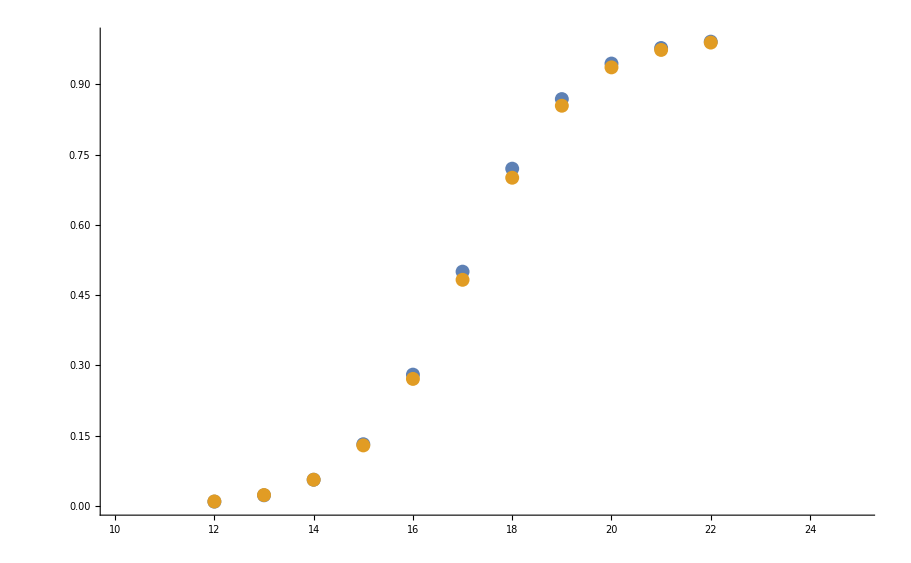

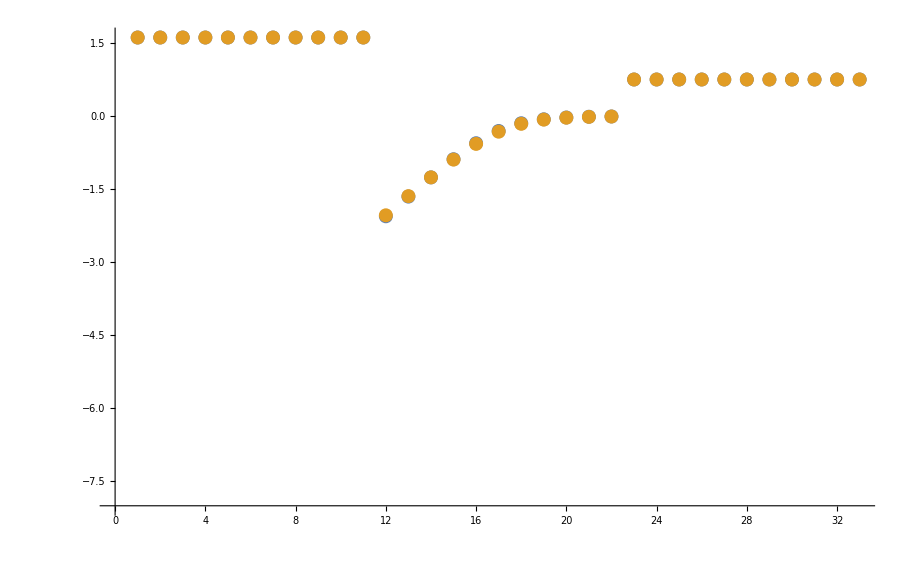

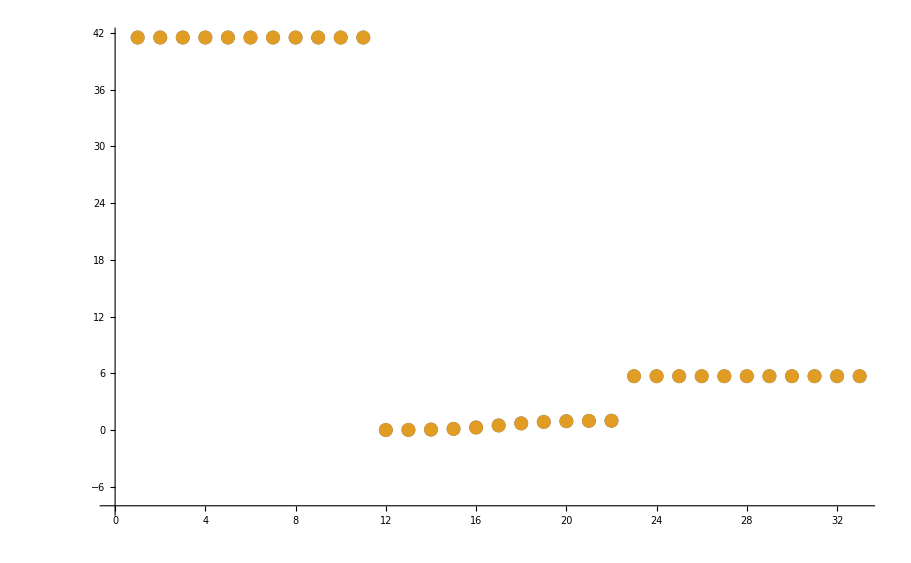

```mathematica
datasetI=20;
ListPlot[{fittingData[[All,-1]], filteredDataList[[datasetI,3]]}, AxesOrigin->{0,-8}, PlotRange->{{10,25}, {0,1}}]
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}, AxesOrigin->{0,-8}]
```

```mathematica
enzymeModel["Reactions"]
```

{((PYK^c)_^+fdp^c⇌(PYK^c&fdp^c)_^)^PYK1,((PYK^c&pi^c)_^→(PYK^c)_^+pi^c)^PYK2,((PYK^c&fdp^c)_^+fdp^c⇌(PYK^c&fdp^c&fdp^c)_^)^PYK3,((PYK^c&pi^c&pi^c)_^→(PYK^c&pi^c)_^+pi^c)^PYK4,((PYK^c&fdp^c&fdp^c)_^→(PYK^c&pi^c&pi^c&f6p^c&f6p^c)_^)^PYK5,((PYK^c&pi^c&pi^c&f6p^c)_^→(PYK^c&pi^c&pi^c)_^+f6p^c)^PYK6,((PYK^c&pi^c&pi^c&f6p^c&f6p^c)_^→(PYK^c&pi^c&pi^c&f6p^c)_^+f6p^c)^PYK7}

### Parameter Distribution



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```



```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```



```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
Get["MASSef`"]
```

```mathematica
backCalculateKms[rxn, s05List,relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

{1,1}

{fdp^c→∞}

fdp^c

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{fdp^c→-0.0000697842},{fdp^c→0.0000701712}}

data value | predicted value | error in %
0.00007 | 0.0000701712 | 0.24454

```mathematica
backCalculateKcats[rxn, kcatList,relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
5.7 | 5.68849 | 0.202015

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]],  paramFitSub]//TableForm
```

data value | predicted value | error in %
41.5 | 41.8494 | 0.841854

```mathematica
f6pCoSub = {pi^c-> assumedSaturatingConc};
piCoSub={f6p^c-> assumedSaturatingConc};
relRatef6p=Values@FilterRules[fileListSub,inputPath <> "/relRateRev_f6p.txt"];
relRatepi=Values@FilterRules[fileListSub,inputPath <> "/relRateRev_pi.txt"];
```

```mathematica
backCalulateKmSimple[relRate_,paramFitSub_,coSub_,substrate_]:=Block[{kmPredicted},

  kmPredicted = Solve[(relRate/.paramFitSub/. coSub)==0.5, substrate];
	kmPredicted = Flatten[Values @ kmPredicted];
  kmPredicted = If[Length[kmPredicted] > 1,
					Flatten[Select[kmPredicted, Head[#] === Real && #> 0  &]][[1]],
					kmPredicted
				];
Return[kmPredicted]
];
```

```mathematica
absoluteRateReverse
```

(2 (f6p^c)^2 (pi^c)^2 FBP2_total_Global k_FBP21^⟵ k_FBP22^⟵ k_FBP23^⟵ k_FBP24^⟵ k_FBP25^⟵ k_FBP26^⟵ k_FBP27^⟵)/((f6p^c)^2 (k_FBP21^⟵ k_FBP22^⟶ k_FBP23^⟵ k_FBP25^⟵+pi^c k_FBP21^⟵ k_FBP23^⟵ (k_FBP22^⟵+k_FBP24^⟵) k_FBP25^⟵+(pi^c)^2 k_FBP22^⟵ k_FBP24^⟵ (k_FBP23^⟵ k_FBP25^⟵+k_FBP21^⟵ (k_FBP23^⟵+k_FBP25^⟵+k_FBP25^⟶))) k_FBP26^⟵ k_FBP27^⟵+k_FBP21^⟵ ((pi^c)^2 k_FBP22^⟵ k_FBP24^⟵+pi^c k_FBP22^⟵ k_FBP24^⟶+k_FBP22^⟶ k_FBP24^⟶) k_FBP26^⟶ (k_FBP25^⟶ k_FBP27^⟶+k_FBP23^⟵ (k_FBP25^⟵+k_FBP27^⟶))+f6p^c k_FBP21^⟵ (pi^c k_FBP22^⟵ k_FBP23^⟵ k_FBP24^⟶ k_FBP25^⟵ k_FBP27^⟵+k_FBP22^⟶ k_FBP23^⟵ k_FBP24^⟶ k_FBP25^⟵ k_FBP27^⟵+(pi^c)^2 k_FBP22^⟵ k_FBP24^⟵ (k_FBP25^⟶ k_FBP26^⟵ k_FBP27^⟶+k_FBP23^⟵ (k_FBP25^⟵ (k_FBP26^⟵+k_FBP27^⟵)+k_FBP26^⟵ k_FBP27^⟶))))

#### Export rate back calculated parameter error distribution

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
nRateSets=100;
rateConstList=Import[outputPath<>"/treated_data/rateconst_FBP2_"<>fitLabel<>"_"<>flagFitType<>".csv", "TSV"];


predictedParamsList=Table[

(*paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[rateSetI,2]]];*)
paramFitSub=Thread[rateConstsSub[[All,1]]->rateConstList[[rateSetI,2;;]]];
km=backCalculateKms[rxn, s05List, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub,paramFitSub, assumedSaturatingConc, rxnName][[2;;,All]];

{filteredDataList[[rateSetI,1]],
km[[All,2]],
backCalulateKmSimple[relRatef6p,paramFitSub,f6pCoSub,f6p^c],
backCalulateKmSimple[relRatepi,paramFitSub,piCoSub,pi^c],
backCalculateHillCoef[{MapThread[{#1,#2}&,{fittingData[[12;;22,3]], filteredDataList[[rateSetI,3]][[12;;22]]}]}, {km[[All,2]]}, otherParmsList][[2,2]],
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc][[2;;,2]],
absoluteRateReverse/.paramFitSub/.Underscript[FBP2_total, Global]-> 1/.{pi^c-> assumedSaturatingConc,f6p^c-> assumedSaturatingConc},
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]],  paramFitSub][[2;;,2]],

Total@Thread[(filteredDataList[[rateSetI,3]][[12;;22]]-allFittingData[[12;;22,-1]])^2],
filteredDataList[[rateSetI,3]][[12;;22]]}//Flatten,
{rateSetI, 1, nRateSets}];

predictedParamsList=Insert[predictedParamsList,{"ssd","S05_fdp","S05_f6p","S05_pi","n_fdp","kcat_f","kcat_r", "Keq","ssd_s05","r1", "r2", "r3", "r4", "r5", "r6", "r7", "r8", "r9", "r10", "r11"} , 1];
predictedParamsList=Insert[predictedParamsList,Flatten@{0,s05List[[1]][[3]],"NA","NA",otherParmsList[[1,4]],kcatList[[1]][[3]],"NA", KeqList[[1]][[3]],0, allFittingData[[12;;22,-1]]}  ,2];;
(*Export[outputPath<>"/treated_data/predicted_params_error_distribution_p10_10000_3.csv",predictedParamsErrorList[[All,;;5]],"CSV"];
Export[outputPath<>"/treated_data/predicted_params_s05_error_distribution_p10_10000_3.csv",predictedParamsErrorList[[All,{1,6,7,8,9,10,11,12,13,14,15, 16,17}]],"CSV"];*)

Export[outputPath<>"/treated_data/predicted_params_distribution_"<>fitLabel<>"_"<>flagFitType<>"_predS05.csv",predictedParamsList[[All,;;8]],"CSV"];
Export[outputPath<>"/treated_data/predicted_params_s05_distribution_"<>fitLabel<>"_"<>flagFitType<>"_predS05.csv",predictedParamsList[[All,{1,6,7,8,9,10,11,12,13,14,15, 16,17}]],"CSV"];

predictedParamsErrorList=Table[

(*paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[rateSetI,2]]];*)
paramFitSub=Thread[rateConstsSub[[All,1]]->rateConstList[[rateSetI,2;;]]];
km=backCalculateKms[rxn, s05List, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub,paramFitSub, assumedSaturatingConc, rxnName][[2;;,All]];

{filteredDataList[[rateSetI,1]],
km[[All,3]],
backCalculateHillCoef[{MapThread[{#1,#2}&,{fittingData[[12;;22,3]], filteredDataList[[rateSetI,3]][[12;;22]]}]}, {km[[All,2]]}, otherParmsList][[2,3]],
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc][[2;;,3]],
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]],  paramFitSub][[2;;,3]],

Total@Thread[(filteredDataList[[rateSetI,3]][[12;;22]]-allFittingData[[12;;22,-1]])^2],
filteredDataList[[rateSetI,3]][[12;;22]]}//Flatten,
{rateSetI, 1, nRateSets}];

predictedParamsErrorList=Insert[predictedParamsErrorList,{"ssd","S05_fdp","n_fdp","kcat_f", "Keq","ssd_s05","r1", "r2", "r3", "r4", "r5", "r6", "r7", "r8", "r9", "r10", "r11"} , 1];
predictedParamsErrorList=Insert[predictedParamsErrorList,Flatten@{0,s05List[[1]][[3]],otherParmsList[[1,4]],kcatList[[1]][[3]], KeqList[[1]][[3]],0, allFittingData[[12;;22,-1]]}  ,2];;


Export[outputPath<>"/treated_data/predicted_params_error_distribution_"<>fitLabel<>"_"<>flagFitType<>".csv",predictedParamsErrorList[[All,;;5]],"CSV"];
Export[outputPath<>"/treated_data/predicted_params_s05_error_distribution_"<>fitLabel<>"_"<>flagFitType<>".csv",predictedParamsErrorList[[All,{1,6,7,8,9,10,11,12,13,14,15, 16,17}]],"CSV"];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.